```mathematica
Quit[]
```

## Backgrounds

```mathematica
(*Debugging Functions*)
On[Assert];
$AssertFunction = Throw[{##}]& ;
```

```mathematica
(*Sensitivity Functions*)
Clear[FindSensitivity];
FindSensitivity[Ndat_,Nbg_,α_,start_,WithCLs_:False]:=Block[{Nsig,CLSDenom},
Assert[Length[Ndat]==Length[Nbg]];

CLSDenom=Table[1,{i,1,Length@Ndat}];
If[WithCLs,
CLSDenom=1-pValuePoissonL[Ndat,0,Nbg];
];

Table[Nsig/.FindRoot[CLSDenom⟦i⟧*α-Gamma[1+Ndat⟦i⟧,Nbg⟦i⟧+Nsig]/Gamma[1+Ndat⟦i⟧,Nbg⟦i⟧](*Credible Interval of Posterior Distributions*),{Nsig,start}],{i,1,Length@Nbg}]
];

Clear[pValuePoissonL];
pValuePoissonL[n_,s_,b_]:=Block[{hello},
Assert[Length[n]==Length[b]];
Table[Sum[(s+b⟦i⟧)^nn/(nn!)Exp[-(s+b⟦i⟧)],{nn,n⟦i⟧,∞}],{i,1,Length@n}]
];
```

### HNLMonophoton Bkg

```mathematica
Data0Jets={1559,379,116,1180,263};
DataIncJets={2400,729,236,1671,493};
Dat0IncEff=Data0Jets/DataIncJets//N
```

{0.649583,0.51989,0.491525,0.706164,0.533469}

```mathematica
BkgIncJets={2600,765,273,1900,501}
```

{2600,765,273,1900,501}

```mathematica
Bkg0Jets=BkgIncJets*Dat0IncEff
```

{1688.92,397.716,134.186,1341.71,267.268}

```mathematica
FindSensitivity[Data0Jets,Bkg0Jets,(1-0.95),2]
```

{32.8133,29.8881,14.6614,22.606,30.9375}

```mathematica
CLSDenom=1-pValuePoissonL[Data0Jets,0,Bkg0Jets]
```

{0.000660138717,0.16776162166698,0.0506923,3.123376×10^-6,0.388864806698513}

```mathematica
(*These are the Nsig that need to be solved for!*)
FindSensitivity[Data0Jets,Bkg0Jets,(1-0.95),3,True]
```

{96.4397,42.6703,25.8965,100.601,37.4494}

### HNLPhotonlepton Bkg

```mathematica
dat=Transpose[Import[NotebookDirectory[]<>"../Backgrounds/PhotonleptonBackgrounds.csv"]]⟦2⟧
```

{24.975,34.112,3.0457,3.0457,0.15228,0.15228,22.843,35.787,3.5025,1.8274,0.30457,0.15228}

```mathematica
Length@dat
```

12

```mathematica
data=Table[dat⟦2i-1⟧+dat⟦2i⟧,{i,1,3}]
```

{59.087,6.0914,0.30456}

```mathematica
Bkg=Table[dat⟦2i-1⟧+dat⟦2i⟧,{i,4,6}]
```

{58.63,5.3299,0.45685}

```mathematica
FindSensitivity[data,Bkg,(1-0.95),2]
```

{17.1434,7.20974,3.39884}

```mathematica
CLSDenom=1-pValuePoissonL[data,0,Bkg]
```

{0.506461,0.573558,0.204357}

```mathematica
(*These are the Nsig that need to be solved for!*)
FindSensitivity[data,Bkg,(1-0.95),6,True]
```

{19.7118,8.16854,5.07888}

## Plotting Sensitivities

DID YOU REMEMBER TO COPY PASTE THE CORRECT Sensitivity FILE INTO THIS FOLDER?

```mathematica
Quit[]
```

```mathematica
Clear[header,stringHeader,HNL1,HNL2,HNL3,HNL4,HNLdat];
header=ToExpression[Import[NotebookDirectory[]<>"outputColumns.csv"]⟦1⟧];
stringHeader=ToString/@header;
HNL1=Sort[ToExpression@Import[NotebookDirectory[]<>"Master.LHCSensitivity.HNLMonoPhoton.13TeV.dscale1.csv"]];
HNL2=Sort[ToExpression@Import[NotebookDirectory[]<>"Master.LHCSensitivity.HNLPhotonLepton.8TeV.dscale0.2.csv"]];
HNL3=Sort[ToExpression@Import[NotebookDirectory[]<>"Master.LHCSensitivity.HNLPhotonLepton.8TeV.dscale1.0.csv"]];
HNL4=Sort[ToExpression@Import[NotebookDirectory[]<>"Master.LHCSensitivity.HNLPhotonLepton.8TeV.dscale5.0.csv"]];
Evaluate[header]=Range[Length[header]];
HNLdat={HNL1,HNL2,HNL3,HNL4,header,stringHeader};
```

### Definition

```mathematica
Clear[PackageHNL]
PackageHNL[dat_,index_]:=Block[{d},
d=Table[{dat⟦i,1⟧,dat⟦i,index⟧},{i,1,Length[dat]}];
Return[d];
];

basicStyles={Joined->True,FrameStyle->18,FrameStyle->Thin,ImageSize->500,InterpolationOrder->1,Frame->True};
Clear[PlotSensitivity];
PlotSensitivity[hnldata_,title_]:=Block[{dat},
Table[
dat=PackageHNL[hnldata,header⟦i⟧];

ListLogLogPlot[dat,FrameLabel->{"HNL Mass [GeV]",stringHeader⟦i⟧},PlotStyle->Back,PlotRange->All,PlotLabel->Style[title,18],basicStyles],{i,dSRBest,Length@header}]

];
```

### Monophoton ATLAS

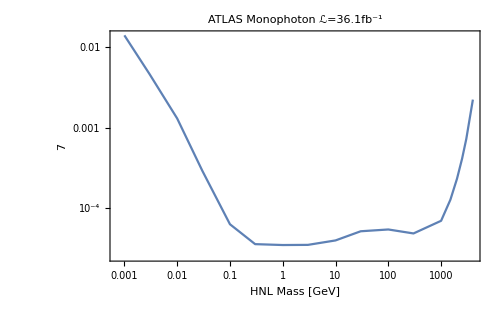
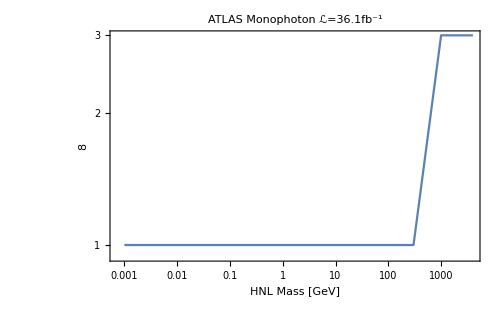
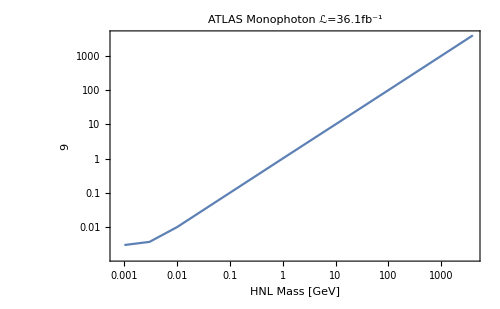
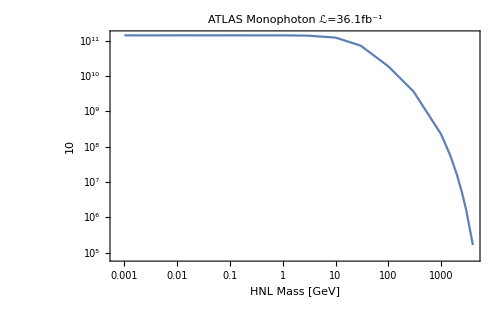
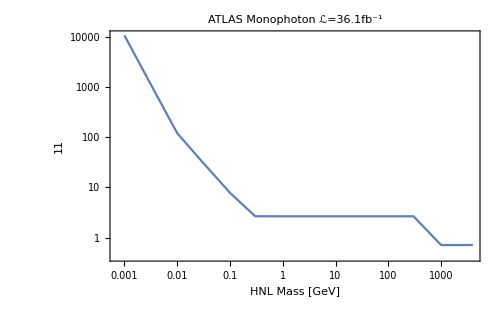
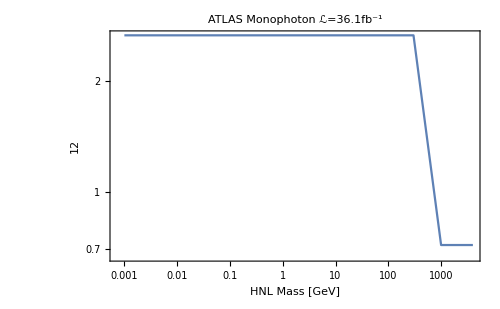
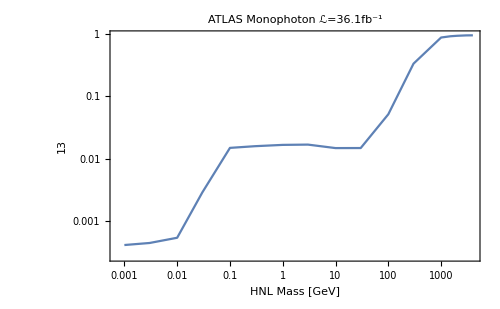
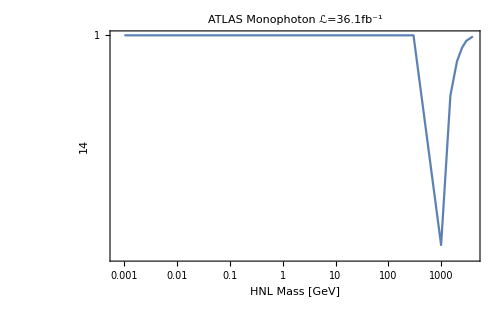

```mathematica
PlotSensitivity[HNLdat⟦1⟧,"ATLAS Monophoton ℒ=36.1fb^-1"]
```

### Photon Lepton CMS

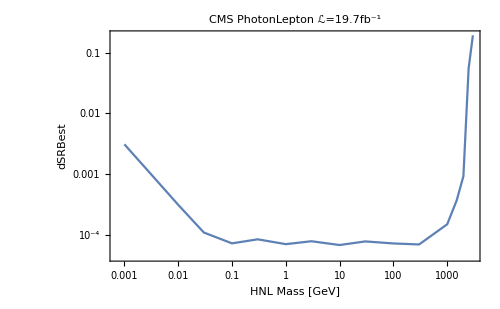
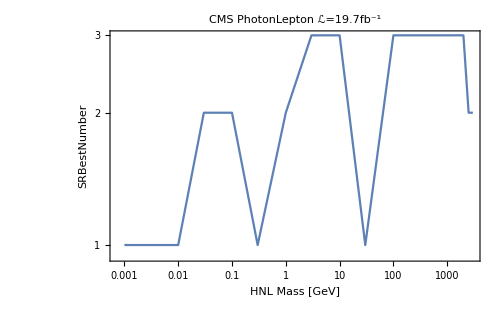
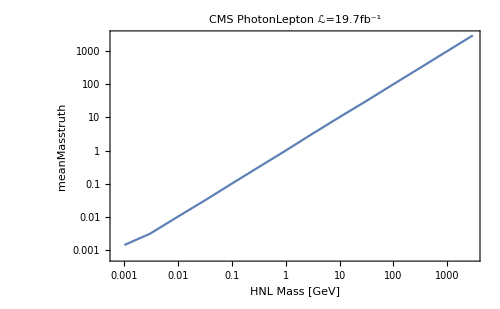
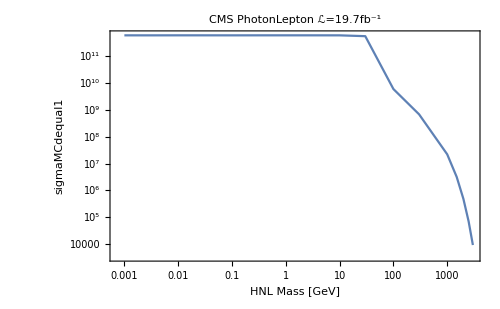
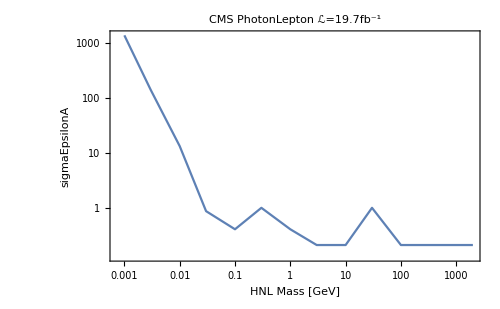
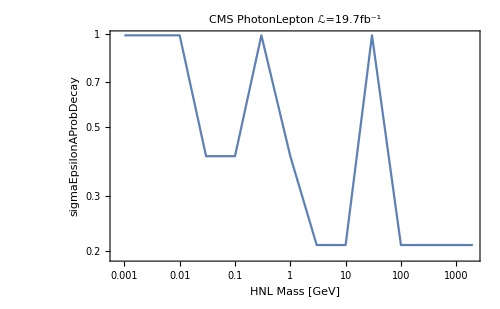
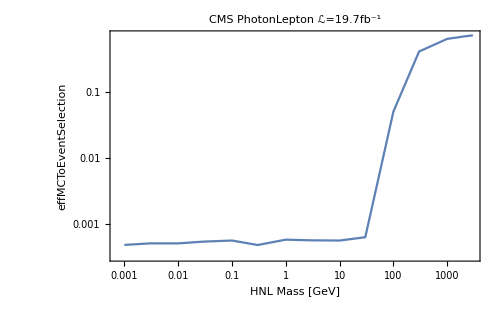
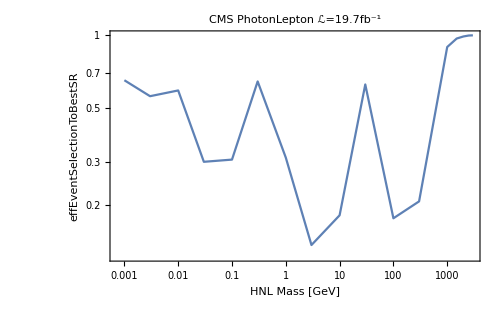

```mathematica
PlotSensitivity[HNLdat⟦4⟧,"CMS PhotonLepton ℒ=19.7fb^-1"]
```

### Export Everything

```mathematica
Export["~/Dropbox/dipole-neutrino-portal/PaperResults/IntermediateResults/LHC.m",HNLdat]
```

~/Dropbox/dipole-neutrino-portal/PaperResults/IntermediateResults/LHC.m